# Protein interaction networks

Proteins interact with other proteins in biological processes as varied as DNA replication, signal transduction, movement of molecules into and between cells, and essentially all processes in living cells. In fact, signal transduction, a process in which protein control the signaling into and out of the cell, is key to the study of diseases including many cancers. Their importance in all cellular activity has given rise to active work in the visualization of protein-protein interactions (PPIs). Here, we will combine functional constructs, pattern matching, and graph tools to visualize nettworks of proteins that have a high level of interaction.

We will work with proteins from the worm Caenorhabditis elegans, a heavily studied organism. The data we used here are from the Center for Cancer Systems Biology at the Dana-Farber Cancer Institute. The data are in the form of a tab-seperated text file (TSV).

```mathematica
data=Import["http://interactome.dfci.harvard.edu/C_elegans/graphs/sequence_edges/wi2007.txt","TSV"];
```

```mathematica
Length[data]
```

1817

```mathematica
Dimensions[data]
```

{1817,2}

When importing data, one of the first things you need to figure out is the nature of what you are working with. 

(1) Two very useful things to know after import are how big is the data set is and what does a typical element look like. Use Length and Dimensions to obtain those information.

(2) The data are of the form {protein_1, protein_2}, which indicates an interaction between these two named proteins. Use Take to show a few representative elements. Again, before apply the whole analysis to the entire data set, use Take to obtain the first 12 elements in the data as a prototype data.

```mathematica
Take[data,12]
```

{{#IDA,IDB},{AC3.3,F29G6.3},{AC3.3,R05F9.10},{AC3.3,Y69H2.3},{AC3.7,Y40B10A.2},{B0001.4,F19B6.1},{B0001.7,B0281.5},{B0001.7,F37H8.1},{B0024.10,C06A1.1},{B0024.12,C06E2.1},{B0024.14,B0228.1},{B0024.14,C05G6.1}}

```mathematica
ToEdges[Take[data,12]]
```

```mathematica
{"#IDA"->"IDB","AC3.3"->"F29G6.3","AC3.3"->"R05F9.10","AC3.3"->"Y69H2.3","AC3.7"->"Y40B10A.2","B0001.4"->"F19B6.1","B0001.7"->"B0281.5","B0001.7"->"F37H8.1","B0024.10"->"C06A1.1","B0024.12"->"C06E2.1","B0024.14"->"B0228.1","B0024.14"->"C05G6.1"}
```

(3) Use the function ToEdges, developed above, we turn these lists into edges, where each edge represents an interaction between two proteins (vertices in the graph). Apply ToEdges to the 12 prototype data.

(4) Notice that ““#IDA”->”IDB”” is meant to be a comment. Remember to delete that entry in your analysis. Let us then apply ToEdges to the rest of the data and call the result as edges.

```mathematica
edges=ToEdges[Rest[data]];
gr=Graph[edges,GraphStyle->"BasicBlue"]
```

-Graphics-

```mathematica
?Graph
```

Graph[{e_1,e_2,…}] yields a graph with edges e_j.
Graph[{v_1,v_2,…},{e_1,e_2,…}] yields the graph with vertices v_i and edges e_j. 
Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

(5) Use Graph to plot the directed graph, and call it gr. For example gr=Graph[edges, GraphStyle→”BasicBlue”]

(6) The graph we obtained in step (5) is a fairly dense graph showing all the protein interactions, and as a result, it is a bit difficult to discern the details. Many of the interactions involve only two proteins. Our task is to find the sub-graph consisting of all those proteins with greater than 12 interactions with other proteins. 

VertexDegree[gr,vertex] gives the number of edges incident to vertex in a graph gr. So in our protein network, the vertex degree for vertex v_i gives the number of interactions between that protein and all other protein. For example,

```mathematica
VertexDegree[gr,"R05F9.10"]
```

86

Which means that the vertex (which is a protein named R05F9.10) interacts with 86 other proteins.

Use SortBy, Tally, VertexDegree to construct a list of odered pairs {{1, 933}, {2, 246}, ... }  where {1, 933} means that, vertices with one edge occur 933 times in this network, and {2, 246}  means that, vertices with two edges occur 246 times, and so on.

(7) Use Select and and appropriate predicate, extract all vertices with vertex degree greater than 12. Put the result in a list and call the list proteins.

```mathematica
SortBy[Tally[VertexDegree[gr]],First]
```

{{1,933},{2,246},{3,107},{4,64},{5,40},{6,21},{7,19},{8,6},{9,10},{10,6},{11,2},{12,11},{13,2},{14,1},{15,2},{16,3},{17,2},{18,2},{19,3},{21,2},{23,1},{24,2},{28,1},{30,1},{31,3},{39,1},{44,1},{45,1},{47,1},{49,1},{86,1}}

```mathematica
Select[VertexList[gr],(VertexDegree[gr,#]>12&)]
```

{R05F9.10,Y69H2.3,Y40B10A.2,DH11.4,K09B11.9,R02F2.5,ZK1053.5,W05H7.4,C18G1.2,T11B7.1,F52E1.7,F46A9.5,Y54E2A.3,ZK858.4,C50F4.1,K12C11.2,C06G1.5,Y65B4BR.4,F32B4.4,ZK849.2,C36C9.1,ZK1055.7,C06A5.9,W09C2.1,F44G3.9,ZK121.2,M04G12.1,T21G5.5,W10C8.2,F01G10.2,Y55F3C.6}

(8) Now, define edges2 to be the list of proteins obtained in Step 7 which interact with each other. In other words, this is a list of all proteins interaction involving proteins that have greater than 12 interactions. Delete those cases which involve proteins self interactions and call the new list gr1.

(Hint: Lookup Cases, and MemberQ, for Cases, try Cases[expr,pattern,levelspec], with levelspec Infinity )

```mathematica
EdgeList[gr]
```

```mathematica
proteins=Select[VertexList[gr],(VertexDegree[gr,#]>12&)]
edges2=Cases[EdgeList[gr],(p1_)];
```

{R05F9.10,Y69H2.3,Y40B10A.2,DH11.4,K09B11.9,R02F2.5,ZK1053.5,W05H7.4,C18G1.2,T11B7.1,F52E1.7,F46A9.5,Y54E2A.3,ZK858.4,C50F4.1,K12C11.2,C06G1.5,Y65B4BR.4,F32B4.4,ZK849.2,C36C9.1,ZK1055.7,C06A5.9,W09C2.1,F44G3.9,ZK121.2,M04G12.1,T21G5.5,W10C8.2,F01G10.2,Y55F3C.6}

```mathematica
edges2=Cases[EdgeList[gr],(p1_->p2_)/;MemberQ[proteins,p1]&&MemberQ[proteins,p2],Infinity]
```

{C06A5.9->C36C9.1,C06A5.9->DH11.4,C06A5.9->F44G3.9,C06G1.5->DH11.4,C06G1.5->F32B4.4,C06G1.5->K09B11.9,C06G1.5->W05H7.4,C06G1.5->Y54E2A.3,C06G1.5->ZK121.2,C06G1.5->ZK849.2,C36C9.1->K09B11.9,C36C9.1->Y54E2A.3,C36C9.1->Y65B4BR.4,C50F4.1->T21G5.5,C50F4.1->W05H7.4,C50F4.1->Y55F3C.6,C50F4.1->ZK849.2,DH11.4->Y65B4BR.4,DH11.4->Y69H2.3,DH11.4->ZK1053.5,F01G10.2->R02F2.5,F01G10.2->W10C8.2,F01G10.2->Y55F3C.6,F01G10.2->ZK121.2,F32B4.4->F32B4.4,F32B4.4->T11B7.1,F32B4.4->W05H7.4,F32B4.4->W10C8.2,F32B4.4->Y54E2A.3,F32B4.4->Y65B4BR.4,F32B4.4->ZK121.2,K09B11.9->W05H7.4,K12C11.2->K12C11.2,K12C11.2->Y55F3C.6,K12C11.2->ZK858.4,M04G12.1->M04G12.1,M04G12.1->ZK849.2,R02F2.5->W10C8.2,R02F2.5->ZK121.2,R02F2.5->ZK858.4,R05F9.10->R05F9.10,R05F9.10->Y65B4BR.4,T11B7.1->ZK121.2,T21G5.5->T21G5.5,W05H7.4->W05H7.4,W05H7.4->Y65B4BR.4,W05H7.4->ZK121.2,W10C8.2->W10C8.2,Y55F3C.6->Y55F3C.6,Y69H2.3->Y69H2.3,ZK1055.7->ZK1055.7,ZK849.2->ZK849.2,ZK858.4->ZK858.4}

```mathematica
gr1=DeleteCases[edges2,x_->x_]
```

{C06A5.9->C36C9.1,C06A5.9->DH11.4,C06A5.9->F44G3.9,C06G1.5->DH11.4,C06G1.5->F32B4.4,C06G1.5->K09B11.9,C06G1.5->W05H7.4,C06G1.5->Y54E2A.3,C06G1.5->ZK121.2,C06G1.5->ZK849.2,C36C9.1->K09B11.9,C36C9.1->Y54E2A.3,C36C9.1->Y65B4BR.4,C50F4.1->T21G5.5,C50F4.1->W05H7.4,C50F4.1->Y55F3C.6,C50F4.1->ZK849.2,DH11.4->Y65B4BR.4,DH11.4->Y69H2.3,DH11.4->ZK1053.5,F01G10.2->R02F2.5,F01G10.2->W10C8.2,F01G10.2->Y55F3C.6,F01G10.2->ZK121.2,F32B4.4->T11B7.1,F32B4.4->W05H7.4,F32B4.4->W10C8.2,F32B4.4->Y54E2A.3,F32B4.4->Y65B4BR.4,F32B4.4->ZK121.2,K09B11.9->W05H7.4,K12C11.2->Y55F3C.6,K12C11.2->ZK858.4,M04G12.1->ZK849.2,R02F2.5->W10C8.2,R02F2.5->ZK121.2,R02F2.5->ZK858.4,R05F9.10->Y65B4BR.4,T11B7.1->ZK121.2,W05H7.4->Y65B4BR.4,W05H7.4->ZK121.2}

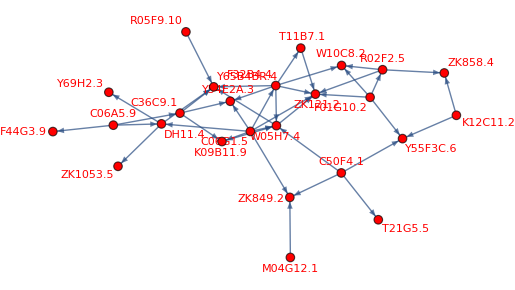

```mathematica
Graph[gr1,VertexStyle->Red,VertexSize->Large,GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
```

(9) Use Graph[gr1,VertexStyle→Red, VertexSize→Large, GraphLayout→”SpringElectricalEmbedding”,VertexLabels→”Name”] to visualize this PPI network.